```mathematica
FourierTransform[Sin[2π t],t,ω]
```

ⅈ √(π/2) DiracDelta[-2 π+ω]-ⅈ √(π/2) DiracDelta[2 π+ω]

```mathematica
ν1=1.0;T1=1/ν1;
ν2=10.0;T2=1/ν2;
ν3=100.0;T3=1/ν3;
tmax=5T2;
dt=T3/10;
data=Table[Sin[2 π ν1 t]+Sin[2π ν2 t]+Sin[2π ν3 t],{t,0,tmax,dt}];
ft=Fourier[data,FourierParameters->{0, 1}];
```

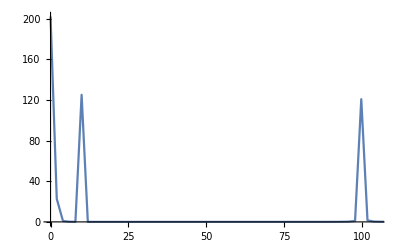

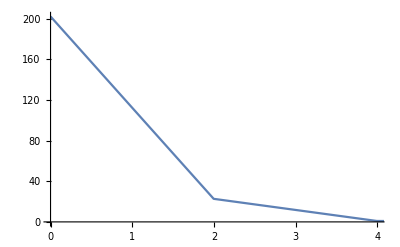

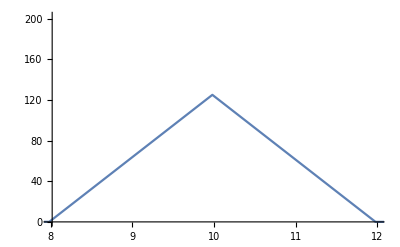

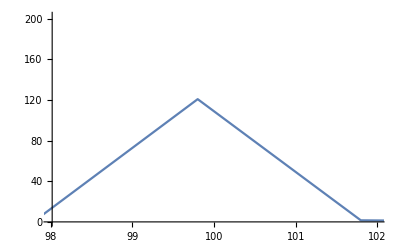

```mathematica
srate=1/dt;
inc=srate/Length[data];
freq=Table[f,{f,0,srate-inc,inc}];
sp=Re[ft]^2+Im[ft]^2;
ListPlot[Transpose[{freq,sp}],PlotRange->{{0,105},Full},Joined->True]
ListPlot[Transpose[{freq,sp}],PlotRange->{{0,4},Full},Joined->True]
ListPlot[Transpose[{freq,sp}],PlotRange->{{8,12},Full},Joined->True]
ListPlot[Transpose[{freq,sp}],PlotRange->{{98,102},Full},Joined->True]
```

```mathematica
π//N
```

3.14159